# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 12: Stiff differential equations 29 APR 2021

## Method implementations.

```mathematica
(*Forward Euler method.*)
fem[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n]},
{x[0],y[0]} = {a,y0};
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*f[x[i],y[i]];,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
(*Classical Runge-Kutta method of order 4.*)
rk4[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n], k1, k2, k3, k4, w1=1./6, w2=1./3, w3=1./3,w4=1./6},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+0.5*h,y[i]+0.5*h*k1];
k3=f[x[i]+0.5*h,y[i]+0.5*h*k2];
k4=f[x[i]+h,y[i]+h*k3];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1+w2*k2+w3*k3+w4*k4);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
(*Backward Euler method.*)
bem[f_,a_,b_,y0_,n_]:=Module[{x,y,yy,h=N[(b-a)/n]},
{x[0],y[0]}={a,y0};
Do[
x[i+1]=x[i]+h;
y[i+1]=yy/.NSolve[yy==y[i]+h*f[x[i],yy]][[1]];,
{i,0,n-1}
];

Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

## A badly behaved example.

Consider the IVP

y’=-200y+200t+101,   y(0)=1.01.

Mathematica easily solves the problem exactly, and since the solution is slowly varying (for the most part), it should pose no problem for our numerical methods.

```mathematica
Clear[t,y]
f[t_,y_]=-200*y+200*t+101;
{t0,y0}={0,1.01};
{a,b}={t0,1};
Y[t_]=FullSimplify[DSolveValue[{y'[t]==f[t,y[t]],y[t0]==y0},y[t],t]];
Print[StringForm["The exact solution to the IVP is ``.",TraditionalForm[y[t]==Y[t]]]];
exactPlot=Plot[Y[t],{t,a,b},AxesLabel->{t,y},PlotStyle->Black,PlotLabels->y[t]==Y[t],ImageSize->Large,PlotLabel->StringForm["``,  ``",y'==f[t,y], y[t0]==y0]]
```

The exact solution to the IVP is y(t)==t+0.51 ⅇ^(-200 t)+0.5.

-Graphics-

However, the usual forward Euler method with step-size h=0.1 is awesomely terrible, and RK4 is even worse!

```mathematica
h=0.1;
n=Round[(b-a)/h];
femSoln=fem[f,a,b,y0,n];
rk4Soln=rk4[f,a,b,y0,n];
mesh=femSoln[[All,1]];
exactY=Y[mesh];
femY=femSoln[[All,2]];
rk4Y=rk4Soln[[All,2]];
TableForm[Join[{mesh,exactY,femY,rk4Y}],TableDirections->Row,TableHeadings->{{"x_i","y(x_i)","FEM y_i", "RK4 y_i"},None},TableSpacing->{2, 2}]
```

x_i | y(x_i) | FEM y_i | RK4 y_i
0 | 1.01 | 1.01 | 1.01
0.1 | 0.6 | -9.09 | 2812.91
0.2 | 0.7 | 184.81 | 1.5508×10^7
0.3 | 0.8 | -3497.29 | 8.55164×10^10
0.4 | 0.9 | 66464.6 | 4.71566×10^14
0.5 | 1. | -1.26281×10^6 | 2.60037×10^18
0.6 | 1.1 | 2.39934×10^7 | 1.43393×10^22
0.7 | 1.2 | -4.55875×10^8 | 7.90717×10^25
0.8 | 1.3 | 8.66162×10^9 | 4.36028×10^29
0.9 | 1.4 | -1.64571×10^11 | 2.4044×10^33
1. | 1.5 | 3.12684×10^12 | 1.32587×10^37

For most of the interval [0,1], the true solution is slowly varying, and so our numerical methods should do a good job.  So, why don’t they?

## Stiffness.

The reason that the above example behaves so poorly is that the desired solution is surrounded by other rapidly decaying transient solutions to the ODE.  The fact that these other solutions converge to our desired solution as t→∞ should help dampen out the errors in our numerical methods, but the problem here is that the convergence is (relatively) too fast.  It is as though the equation is too stable causing the numerical method to become unstable.  This condition is known as stiffness.  “Physically, stiffness corresponds to a process whose components have highly disparate time scales or a process whose time scale is very short compared to the interval over which it is being studied (Heath. Scientific Computing, 2e., 2002).”

Below we give a plot of the desired solution to the above IVP together with several other solutions to the ODE (with different initial value conditions) on top of a direction field.  The slopes of these other solutions are very steep at locations very near the desired solution.

```mathematica
solnFamily=Table[DSolveValue[{y'[t]==f[t,y[t]],y[femSoln[[k,1]]]==femSoln[[k,2]]},y[t],t],{k,1,Length[femSoln]}];
familyPlot=Plot[solnFamily,{t,a,b},PlotRange->{0,1.6}];

Show[
exactPlot,
VectorPlot[{1,f[t,y]},{t,a,b},{y,0,1.5},VectorColorFunction->None,VectorStyle->{Arrowheads[0],Gray}],
familyPlot,
ImageSize->Large,
PlotLabel->StringForm["Solution to the IVP\n ``,  ``\nwith several other solutions to the ODE.",y[t]==Y[t],y[t0]==y0]
]
```

-Graphics-

If we plot the first 4 points of the Euler method approximation together with each corresponding tangent line, we can see why this situation would tend to “confuse” the forward Euler method (or really any explicit method).  An explicit method would require a very short step-size h in order to avoid drastically over-shooting its target.

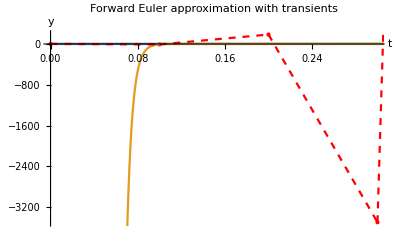

```mathematica
B=4;
Show[
ListPlot[femSoln[[;;B]],PlotStyle->{PointSize[Large],Red}],
Plot[Y[t],{t,a,b},PlotRange->150],
Plot[solnFamily,{t,a,b}],
ParametricPlot[Table[{femSoln[[k,1]],femSoln[[k,2]]}*(1-t)+{femSoln[[k+1,1]],femSoln[[k+1,2]]}*t,{k,1,B}],{t,0,1},PlotStyle->{Dashed,Red}],
PlotLabel->"Forward Euler approximation with transients",
AxesLabel->{t,y}
]
```

For this reason, stiff differential equations are best solved using implicit methods, which tend to be much less sensitive to small perturbations in initial conditions.  By their very nature, implicit methods require the an equation solving subroutine.  Typically, Newton’s method or some variant is used.  The simplest implicit numerical method is the backward Euler method.  For our implementation of the method, we have used Mathematica’s built-in routine NSolve.  Observe that the backward Euler method has no trouble with the toy problem that has so stymied both forward Euler and RK4.

```mathematica
h=0.1;
n=Round[(b-a)/h];
bemSoln=bem[f,a,b,y0,n];
mesh=bemSoln[[All,1]];
exactY=Y[mesh];
bemY=bemSoln[[All,2]];
TableForm[Join[{mesh,exactY,femY,bemY}],TableDirections->Row,TableHeadings->{{"x_i","y(x_i)","FEM y_i", "BEM y_i"},None},TableSpacing->{2, 2}]
```

x_i | y(x_i) | FEM y_i | BEM y_i
0 | 1.01 | 1.01 | 1.01
0.1 | 0.6 | -9.09 | 0.529048
0.2 | 0.7 | 184.81 | 0.601383
0.3 | 0.8 | -3497.29 | 0.700066
0.4 | 0.9 | 66464.6 | 0.800003
0.5 | 1. | -1.26281×10^6 | 0.9
0.6 | 1.1 | 2.39934×10^7 | 1.
0.7 | 1.2 | -4.55875×10^8 | 1.1
0.8 | 1.3 | 8.66162×10^9 | 1.2
0.9 | 1.4 | -1.64571×10^11 | 1.3
1. | 1.5 | 3.12684×10^12 | 1.4